```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/work/factorial_cumulant/fRG-QM

## mub=0 B fluc normal Vglue

```mathematica
chi2v2mub0=Flatten[Import["./v2/mub0PQM_fluc/final/buffer/chi2.dat"]];
chi4v2mub0=Flatten[Import["./v2/mub0PQM_fluc/final/buffer/chi4.dat"]];
r42v2mub0=chi4v2mub0/chi2v2mub0;
```

## mub=0 B fluc baryon Vglue

```mathematica
chi2v1mub0=Flatten[Import["./v1/mub0PQM_fluc/final/buffer/chi2.dat"]];
chi4v1mub0=Flatten[Import["./v1/mub0PQM_fluc/final/buffer/chi4.dat"]];
r42v1mub0=chi4v1mub0/chi2v1mub0;
```

## mub=0 net-B fluc

```mathematica
chi2netBmub0=Flatten[Import["./v2/chiB/mub0/final/buffer/chi2.dat"]];
chi4netBmub0=Flatten[Import["./v2/chiB/mub0/final/buffer/chi4.dat"]];
r42netBmub0=chi4netBmub0/chi2netBmub0;
```

## mub=600 B fluc normal Vglue

```mathematica
chi2v2mub600=Flatten[Import["./v2/finitemub/mub600/final/buffer/chi2.dat"]];
chi4v2mub600=Flatten[Import["./v2/finitemub/mub600/final/buffer/chi4.dat"]];
r42v2mub600=chi4v2mub600/chi2v2mub600;
```

## mub=600 B fluc baryon Vglue

```mathematica
chi2v1mub600=Flatten[Import["./v1/finitemub_PQM/flucP/mub600/final/buffer/chi2.dat"]];
chi4v1mub600=Flatten[Import["./v1/finitemub_PQM/flucP/mub600/final/buffer/chi4.dat"]];
r42v1mub600=chi4v1mub600/chi2v1mub600;
```

## mub=600 net-B fluc

```mathematica
chi2netBmub600=Flatten[Import["./v2/chiB/mub600/final/buffer/chi2.dat"]];
chi4netBmub600=Flatten[Import["./v2/chiB/mub600/final/buffer/chi4.dat"]];
r42netBmub600=chi4netBmub600/chi2netBmub600;
```

## Plot

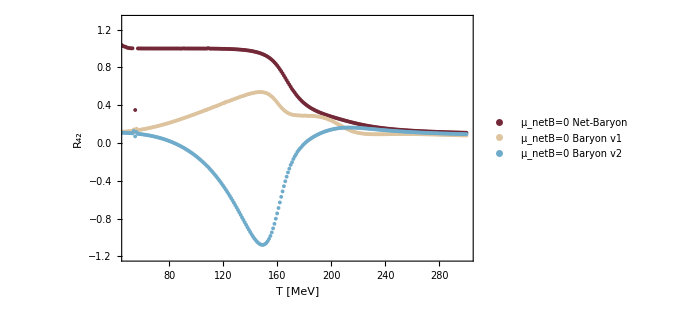

```mathematica
plotR42mub0=ListPlot[{r42netBmub0,r42v1mub0,r42v2mub0},
Frame->True,FrameLabel->{Style["T [MeV]",25,FontFamily->"Times",Black],Style["R_42",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.4}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_netB=0 Net-Baryon","μ_netB=0 Baryon v1","μ_netB=0 Baryon v2"},LabelStyle->16],{0.8,0.25}],
PlotRange->{{50,300},{-1.2,1.3}},AxesOrigin->{0,0},FrameTicksStyle->Directive[15,Black],ImageSize->500]
```

```mathematica
Export["./R42_T.pdf",plotR42mub0]
```

./R42_T.pdf

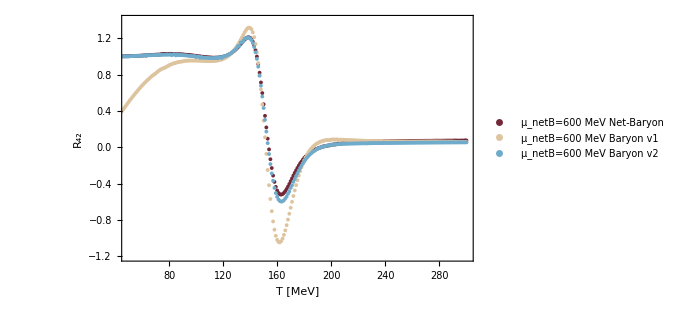

```mathematica
plotR42mub600=ListPlot[{r42netBmub600,r42v1mub600,r42v2mub600},
Frame->True,FrameLabel->{Style["T [MeV]",25,FontFamily->"Times",Black],Style["R_42",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.4}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_netB=600 MeV Net-Baryon","μ_netB=600 MeV Baryon v1","μ_netB=600 MeV Baryon v2"},LabelStyle->16],{0.7,0.75}],
PlotRange->{{50,300},{-1.2,1.4}},AxesOrigin->{0,0},FrameTicksStyle->Directive[15,Black],ImageSize->500]
```

```mathematica
Export["./R42_Tmub600.pdf",plotR42mub600]
```

./R42_Tmub600.pdf

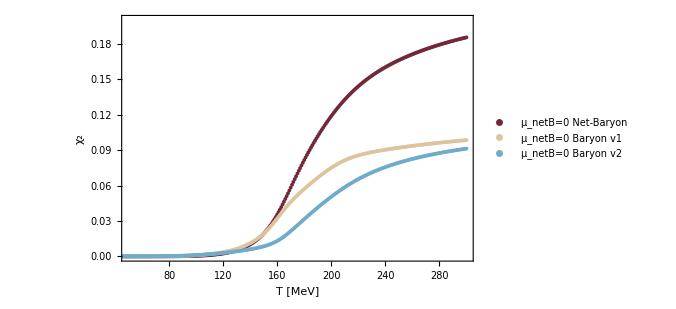

```mathematica
plotchi2mub0=ListPlot[{chi2netBmub0,chi2v1mub0,chi2v2mub0},
Frame->True,FrameLabel->{Style["T [MeV]",25,FontFamily->"Times",Black],Style["χ_2",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.4}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_netB=0 Net-Baryon","μ_netB=0 Baryon v1","μ_netB=0 Baryon v2"},LabelStyle->16],{0.3,0.75}],
PlotRange->{{50,300},{0,0.2}},AxesOrigin->{0,0},FrameTicksStyle->Directive[15,Black],ImageSize->500]
```

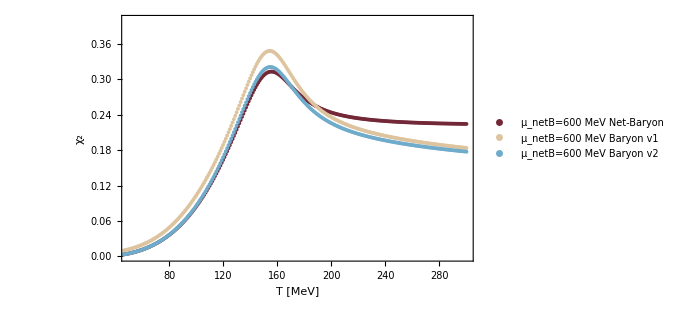

```mathematica
plotchi2mub600=ListPlot[{chi2netBmub600,chi2v1mub600,chi2v2mub600},
Frame->True,FrameLabel->{Style["T [MeV]",25,FontFamily->"Times",Black],Style["χ_2",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.4}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_netB=600 MeV Net-Baryon","μ_netB=600 MeV Baryon v1","μ_netB=600 MeV Baryon v2"},LabelStyle->16],{0.6,0.3}],
PlotRange->{{50,300},{0,0.4}},AxesOrigin->{0,0},FrameTicksStyle->Directive[15,Black],ImageSize->500]
```

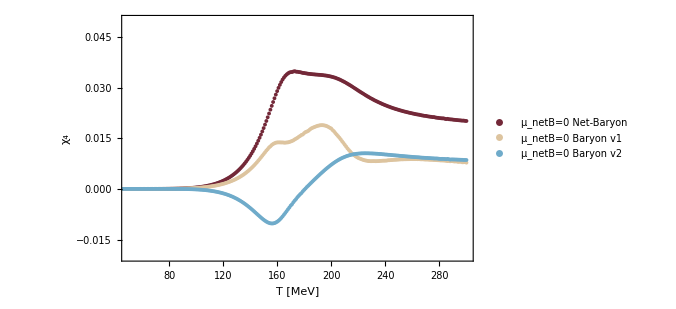

```mathematica
plotchi4mub0=ListPlot[{chi4netBmub0,chi4v1mub0,chi4v2mub0},
Frame->True,FrameLabel->{Style["T [MeV]",25,FontFamily->"Times",Black],Style["χ_4",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.4}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_netB=0 Net-Baryon","μ_netB=0 Baryon v1","μ_netB=0 Baryon v2"},LabelStyle->16],{0.25,0.75}],
PlotRange->{{50,300},{-0.02,0.05}},AxesOrigin->{0,0},FrameTicksStyle->Directive[15,Black],ImageSize->500]
```

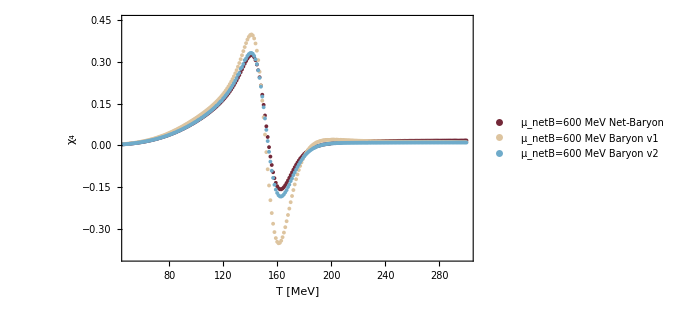

```mathematica
plotchi4mub600=ListPlot[{chi4netBmub600,chi4v1mub600,chi4v2mub600},
Frame->True,FrameLabel->{Style["T [MeV]",25,FontFamily->"Times",Black],Style["χ_4",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.4}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_netB=600 MeV Net-Baryon","μ_netB=600 MeV Baryon v1","μ_netB=600 MeV Baryon v2"},LabelStyle->16],{0.7,0.7}],
PlotRange->{{50,300},{-0.4,0.45}},AxesOrigin->{0,0},FrameTicksStyle->Directive[15,Black],ImageSize->500]
```

```mathematica
Export["./chi2_Tmub0.pdf",plotchi2mub0]
Export["./chi2_Tmub600.pdf",plotchi2mub600]
Export["./chi4_Tmub0.pdf",plotchi4mub0]
Export["./chi4_Tmub600.pdf",plotchi4mub600]
```

./chi2_Tmub0.pdf

./chi2_Tmub600.pdf

./chi4_Tmub0.pdf

./chi4_Tmub600.pdf

## Plot freeze-out

```mathematica
r21facv1=Import["./v1/finitemub_PQM/R21fac.dat"];
r21facv2=Import["./v2/finitemub/R21fac.dat"];
r41facv1=Import["./v1/finitemub_PQM/R41fac.dat"];
r41facv2=Import["./v2/finitemub/R41fac.dat"];
r31facv1=Import["./v1/finitemub_PQM/R31fac.dat"];
r31facv2=Import["./v2/finitemub/R31fac.dat"];
```

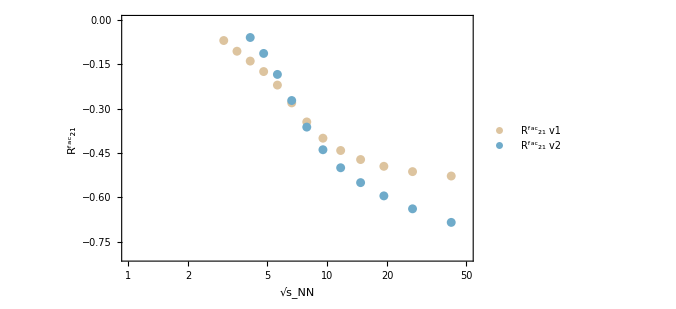

```mathematica
plotR21fac=ListPlot[{r21facv1,r21facv2},
Frame->True,FrameLabel->{Style["√s_NN",25,FontFamily->"Times",Black],Style["(R^fac)_21",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0.4,1,0.4}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"(R^fac)_21 v1","(R^fac)_21 v2"},LabelStyle->16],{0.3,0.25}],
PlotRange->{{1,50},{-0.8,0.}},AxesOrigin->{0,0},FrameTicksStyle->Directive[15,Black],ScalingFunctions->{"Log"},ImageSize->500]
```

```mathematica
Export["./R21fac.pdf",plotR21fac]
```

./R21fac.pdf

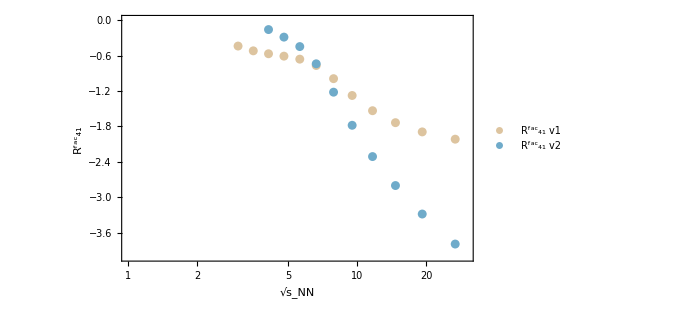

```mathematica
plotR41fac=ListPlot[{r41facv1,r41facv2},
Frame->True,FrameLabel->{Style["√s_NN",25,FontFamily->"Times",Black],Style["(R^fac)_41",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[4.]],{i,0.4,1,0.4}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"(R^fac)_41 v1","(R^fac)_41 v2"},LabelStyle->16],{0.3,0.25}],
PlotRange->{{1,30},{-4.,0.}},AxesOrigin->{0,0},FrameTicksStyle->Directive[15,Black],ScalingFunctions->{"Log"},ImageSize->500]
```

```mathematica
Export["./R41fac.pdf",plotR41fac]
```

./R41fac.pdf

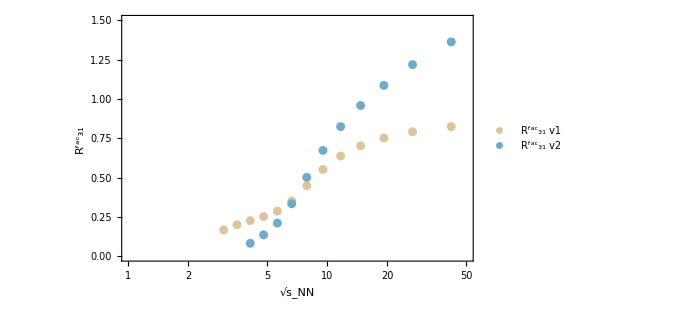

```mathematica
plotR31fac=ListPlot[{r31facv1,r31facv2},
Frame->True,FrameLabel->{Style["√s_NN",25,FontFamily->"Times",Black],Style["(R^fac)_31",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[4.]],{i,0.4,1,0.4}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"(R^fac)_31 v1","(R^fac)_31 v2"},LabelStyle->16],{0.3,0.8}],
PlotRange->{{1,50},{0.,1.5}},AxesOrigin->{0,0},FrameTicksStyle->Directive[15,Black],ScalingFunctions->{"Log"},ImageSize->500]
```

```mathematica
Export["./R31fac.pdf",plotR31fac]
```

./R31fac.pdf